```mathematica
(* ex 3 *)
f[x_]:=x/(1+x)
s[x_]:={x,(f[1]-f[x])/(1-x)}
s[{1.5,1.1,1.01,1.001}]
```

{{1.5,1.1,1.01,1.001},{0.2,0.238095,0.248756,0.249875}}

{0.5,0.333333}

{1.5,0.2}

0.2

0.250125

0.251256

0.263158

0.333333

{0.142857,0.16129,0.163934,0.166113,0.166389,0.166611,0.172414,0.169492,0.167224,0.166945,0.166722}

{0.142857,0.16129,0.163934,0.166113,0.166389,0.166611,0.172414,0.169492,0.167224,0.166945,0.166722}

0.142857

{0.142857,0.16129,0.163934,0.166113,0.166389,0.166611,0.172414,0.169492,0.167224,0.166945,0.166722}

0.142857

{0.142857,0.16129,0.163934,0.166113,0.166389,0.166611,0.172414,0.169492,0.167224,0.166945,0.166722}

0.142857

s[{2.5,2.1,2.05,2.01,2.005,2.001,1.9,1.95,1.99,1.995,1.999}]

s[2.5]

s[{2.5,2.1,2.05,2.01,2.005,2.001,1.9,1.95,1.99,1.995,1.999}]

s[{2.5,2.1,2.05,2.01,2.005,2.001,1.9,1.95,1.99,1.995,1.999}]

{0.714286,0.677419,0.672131,0.667774,0.667221,0.666778,0.655172,0.661017,0.665552,0.66611,0.666556}

12.5

```mathematica
(* ex 19 *)
Limit[(E^x-1-x)/x^2,x->0]
```

1/2

```mathematica
(* ex 21 *)
Limit[(Sqrt[x+4]-2)/x,x->0]
```

1/4

-∞

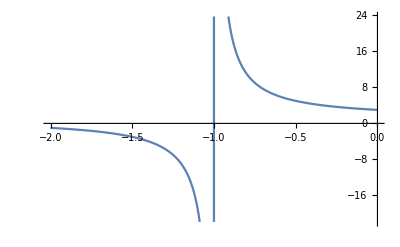

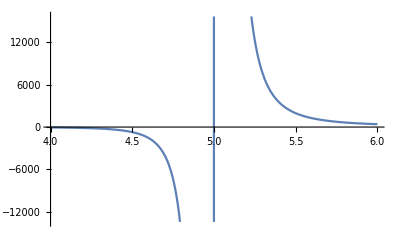

```mathematica
(* ex 25 *)
f[x_]:=(x+3)/(x+1)
Limit[f[x],x->-1,Direction->1]
Plot[{f[x]},{x,-2,0}]
```

```mathematica
Limit[Log[x^2-9],x->3,Direction->1]
```

-∞

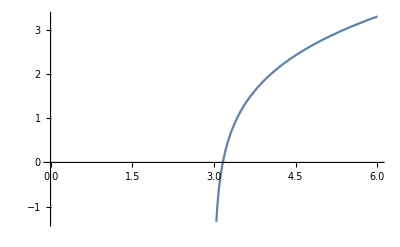

```mathematica
Plot[Log[x^2-9],{x,0,6}]
```